```mathematica
rawData=(****INPUT NEEDED****)(*need file name/location*)Import["/Users/4tc/Dropbox/suli 2018 project/y_optics_0001/input-dist.mu.txt","Table"];
(*Import["/Users/4tc/Dropbox/suli 2018 project/FromJeff/ExtractedBeam/Beam_Correlated.txt","Table"];
rawData=rawData[[;;5000]];*)
correlationData=Drop[Transpose[rawData],-2];
numLines=Length@correlationData[[1]];
averages={Mean[correlationData[[1]]],Mean[correlationData[[2]]],Mean[correlationData[[3]]],Mean[correlationData[[4]]]};
(*order: x, xp, y, yp*)
sigMeasMat={{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}};
mod1=Module[{i,j,k},
For[j=1,j≤4,j++,
For[k=1,k≤4,k++,
sigMeasMat[[k,j]]=(1/numLines)*∑_(i=1)^numLines ((correlationData[[k,i]]-averages[[k]])(correlationData[[j,i]]-averages[[j]]));
];
];]
averages
sigMeasMat=sigMeasMat;  (*convert to mm from m*)
sigMeasMat//MatrixForm  (*COVARIANCE*)

sigX=(sigMeasMat[[1,1]])^(1/2); sigXP=(sigMeasMat[[2,2]])^(1/2); sigY=(sigMeasMat[[3,3]])^(1/2); sigYP=(sigMeasMat[[4,4]])^(1/2);
sigList={sigX,sigXP,sigY,sigYP} 
sigMeasMat2=Table[
sigMeasMat[[m,n]]/(sigList[[m]]*sigList[[n]])
,{m,1,4}
,{n,1,4}
];
MatrixForm@sigMeasMat2 (*PEARSON CORRELATIONS*)

(*MatrixForm[(final4D-sigMeasMat)/sigMeasMat*100]*)
(*Correlation[correlationData[[1]],correlationData[[4]]]*)
```

{-0.000017091,5.63853×10^-6,0.000215628,-0.000017091}

(0.000238531 | 0.0000808269 | -5.14781×10^-7 | 0.000238531
0.0000808269 | 0.0000278103 | -4.66453×10^-8 | 0.0000808269
-5.14781×10^-7 | -4.66453×10^-8 | 0.000133877 | -5.14781×10^-7
0.000238531 | 0.0000808269 | -5.14781×10^-7 | 0.000238531)

{0.0154445,0.00527355,0.0115705,0.0154445}

(1. | 0.992386 | -0.00288069 | 1.
0.992386 | 1. | -0.000764454 | 0.992386
-0.00288069 | -0.000764454 | 1. | -0.00288069
1. | 0.992386 | -0.00288069 | 1.)

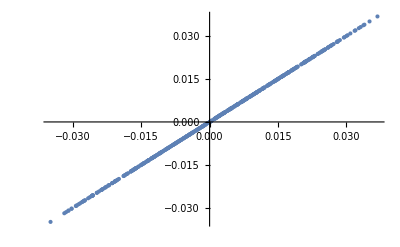

```mathematica
ListPlot[
rawData[[;;;;10,{1,4}]]
]
```

```mathematica
ListPlot[
Import[dataWSD[[1]],"Table"][[;;,{2,3}]]
]
```

Part::partd: Part specification dataWSD⟦1⟧ is longer than depth of object.

Import::chtype: First argument dataWSD⟦1⟧ is not a valid file, directory, or URL specification.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

ListPlot::lpn: Symbol[] is not a list of numbers or pairs of numbers.

ListPlot[Symbol[]]